## Интеграл Лапласа Баталов С.А.

```mathematica
ClearAll["Global`*"]
```

### Начальные данные

```mathematica
ϕ=Log[1+x+x^2];
ψ=Exp[-λ*x^2];
f=ϕ*ψ;
f//TraditionalForm
```

ⅇ^(λ (-x^2)) log(x^2+x+1)

### Решение

Для решения задачи достаточно разложить логарифм в подынтегральном выражении в ряд по степеням аргумента  в окрестности точки , где “сконцентрирован” носитель второго подынтегрального множителя . Не умаляя общности, запишем логарифм с точностью до члена 8-го порядка малости.

```mathematica
Φ=Normal[Series[ϕ,{x,0,8}]];
Φ//TraditionalForm
```

x^8/8+x^7/7-x^6/3+x^5/5+x^4/4-(2 x^3)/3+x^2/2+x

Отметим, что поведение приближающего полинома на бесконечности нас не интересует, так как экспоненциальный множитель заведомо уничтожит полином сколь угодно большой степени. Тогда оценим поведение приближающего многочлена вблизи точки , полагая, что аргумент  достаточно велик.

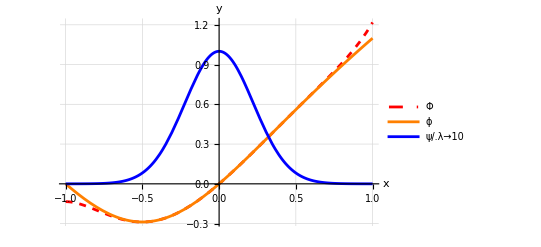

```mathematica
Plot[{Φ,ϕ,ψ/.λ->10},{x,-1,1},PlotLegends->Placed["Expressions",Below],AxesLabel->{x,y},GridLines->Automatic,PlotStyle->{{Red,Dashed},Orange,Blue}]
```

В окрестности нуля полином с высокой степенью точности приближает логарифм, что позволяет нам задействовать его в асимптотическом приближении. Теперь достаточно проинтегрировать произведение полинома и экспоненты, это нетрудно сделать, используя формулу интегрирования по частям и свойства гамма-функции Эйлера.

```mathematica
Int=Integrate[Φ*ψ,{x,-Infinity,Infinity},Assumptions->{λ>1}];
Ans=Expand[Int]+O[λ,Infinity]^(11/2);
Ans//TraditionalForm
```

1/4 √π (1/λ)^(3/2)+3/16 √π (1/λ)^(5/2)-5/8 √π (1/λ)^(7/2)+105/128 √π (1/λ)^(9/2)+O((1/λ)^(11/2))